```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Github\VM2D\settings\wakes

```mathematica
dat=StringSplit[Import["wake1602","Text"],"\n"];
```

```mathematica
Length[dat]
```

1617

```mathematica
dat[[1;;14]]
```

{/*--------------------------------*- VM2D -*-----------------*---------------*\,| ##  ## ##   ##  ####  #####   |                            | Version 1.12   |,| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2024/01/14     |,| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*,|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |,|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |,|                                                                             |,| Copyright (C) 2017-2024 I. Marchevsky, K. Sokol, E. Ryatina, A. Kolganova   |,*-----------------------------------------------------------------------------*,| File name: wake1628                                                         |,| Info: Wake from Kadr (1628 vortices)                                        |,\*---------------------------------------------------------------------------*/,,vtx = {}

```mathematica
pts=Flatten[StringCases[#,___~~"{"~~x__~~","~~y__~~","~~g__~~"}"~~___:>ToExpression@{x,y,g}]&/@(dat[[15;;-2]]),1]
```

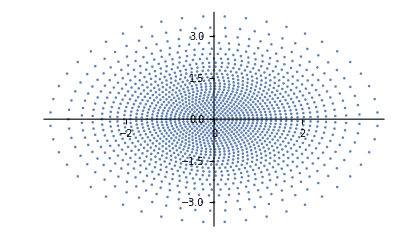

```mathematica
ListPlot[pts[[All,{1,2}]]]
```

```mathematica
shift={15,0};
```

```mathematica
pts2={#[[1]]+shift[[1]],#[[2]]+shift[[2]],#[[3]]}&/@pts;
```

```mathematica
wake=pts~Join~pts2;
```

```mathematica
n=Length@wake;
```

```mathematica
Export["wake"<>ToString[n/2]<>"x2",
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.12   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2024/01/14     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2024 I. Marchevsky, K. Sokol, E. Ryatina, A. Kolganova   |
*-----------------------------------------------------------------------------*
| File name: wake"<>ToString[n/2]<>"x2"<>StringRepeat[" ",59-StringLength@ToString[n]]<>"|
| Info: Two vortices ("<>ToString[n/2]<>" vortices each)"<>StringRepeat[" ",41-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"vtx = {"}
~Join~
Table[{"{",wake[[i,1]],",",wake[[i,2]],",",wake[[i,3]],"},"},{i,Length[wake]-1}]
(*~Join~
Table[{"{",wake[[i,1]],",",wake[[i,2]]+5,",",wake[[i,3]],"},"},{i,Length[wake]-1}]
~Join~
Table[{"{",wake[[i,1]],",",wake[[i,2]]+10,",",wake[[i,3]],"},"},{i,Length[wake]-1}]
~Join~
Table[{"{",wake[[i,1]],",",wake[[i,2]]+15,",",wake[[i,3]],"},"},{i,Length[wake]-1}]*)
~Join~
{{"{",wake[[-1,1]],",",wake[[-1,2]],",",wake[[-1,3]],"},"}}
(*~Join~
{{"{",wake[[-1,1]],",",wake[[-1,2]]+5,",",wake[[-1,3]],"},"}}
~Join~
{{"{",wake[[-1,1]],",",wake[[-1,2]]+10,",",wake[[-1,3]],"},"}}
~Join~
{{"{",wake[[-1,1]],",",wake[[-1,2]]+15,",",wake[[-1,3]],"}"}}*)
~Join~{{" };"}},"Table"]
```

wake1602x2